```mathematica
V[r_] = -ebar^2/r
r0 = 1/(4ebar^2)
```

-ebar^2/r

1/(4 ebar^2)

```mathematica
perturbationterms[x_] = Collect[Simplify[(x (720-360 x^2+120 r0^5 x^2 Derivative[3][V][r0]))/(720 √k)]+Simplify[(x (-1080 x+450 x^3+30 r0^6 x^3 Derivative[4][V][r0]))/(720 k)]+Simplify[(x (-540+1440 x^2-540 x^4+6 r0^7 x^4 Derivative[5][V][r0]))/(720 k^(3/2))]+Simplify[(x (810 x-1800 x^3+630 x^5+r0^8 x^5 Derivative[6][V][r0]))/(720 k^2)],k]
```

-(x (-4+x^2))/(4 √k)+(3 x^2 (-4+x^2))/(8 k)-(x (3-8 x^2+2 x^4))/(4 k^(3/2))+(x^2 (9-20 x^2+5 x^4))/(8 k^2)

```mathematica
∂_x %1
```

(x (-6 x+2 r0^5 x V^(3)[r0]))/(6 √k)+(6-3 x^2+r0^5 x^2 V^(3)[r0])/(6 √k)+(x^2 (30 x+2 r0^6 x V^(4)[r0]))/(24 k)+(x (-36+15 x^2+r0^6 x^2 V^(4)[r0]))/(12 k)+(x (-30 (-16 x+12 x^3)+4 r0^7 x^3 V^(5)[r0]))/(120 k^(3/2))+(-30 (3-8 x^2+3 x^4)+r0^7 x^4 V^(5)[r0])/(120 k^(3/2))+(90 x^2 (-40 x+28 x^3)+180 x (9-20 x^2+7 x^4)+6 r0^8 x^5 V^(6)[r0])/(720 k^2)

```mathematica
w= Sqrt[3/4 + r0^4 V''[r0]]
ezero = 3/(8 k) + r0^2*k*V[r0]-1/2+k/8
```

1/2

-1/2+3/(8 k)-k/8

```mathematica
psizerozero[x_] = (w/(2Pi))^(1/4)Exp[-w*x^2/4]
```

(ⅇ^(-x^2/8))/(√2 π^(1/4))

```mathematica
lambdazerozero = ezero + 1/2 w
```

-1/4+3/(8 k)-k/8

```mathematica
lambdazeroone =Assuming[ √(3+4 r0^4 V''[r0])>0,Integrate[perturbationterms[x]*psizerozero[x]*psizerozero[x],{x,-Infinity,Infinity}]]
```

(3 (63+2 k))/(4 k^2)

```mathematica
lambda =Collect[lambdazeroone + lambdazerozero,l]
```

-1/2+3/(8 k)+k/8+k r0^2 V[r0]+1/2 √(3/4+r0^4 V''[r0])+(1341-108 k-36 (-3+4 k) r0^4 V''[r0]-360 √(3+4 r0^4 V''[r0])+90 k √(3+4 r0^4 V''[r0])+6 k r0^6 √(3+4 r0^4 V''[r0]) V^(4)[r0]+2 r0^8 V^(6)[r0])/(12 k^2 (3+4 r0^4 V''[r0])^(3/2))

```mathematica
21/4
```

21/4

```mathematica
-1/4+3/(8 k)-k/8+(3 (323+8 k) π^(1/4))/k^2
```

-1/2+(347 π^(1/4))/3

```mathematica
ebar = e/k
Energy = Collect[k/r0^2 lambda,k]
```

e/k

(k^2 (1/8+r0^2 V[r0]))/r0^2+(k (-1/2+1/2 √(3/4+r0^4 V''[r0])))/r0^2+(3/8-9/((3+4 r0^4 V''[r0])^(3/2))-(12 r0^4 V''[r0])/((3+4 r0^4 V''[r0])^(3/2))+15/(2 (3+4 r0^4 V''[r0]))+(r0^6 V^(4)[r0])/(2 (3+4 r0^4 V''[r0])))/r0^2+(447/(4 (3+4 r0^4 V''[r0])^(3/2))+(9 r0^4 V''[r0])/((3+4 r0^4 V''[r0])^(3/2))-30/(3+4 r0^4 V''[r0])+(r0^8 V^(6)[r0])/(6 (3+4 r0^4 V''[r0])^(3/2)))/(k r0^2)

```mathematica
8 ebar^4 (-1/2+(347 π^(1/4))/3)
```

```mathematica
a = 8/81 e^4 (-3+694 π^(1/4))
```

8/81 e^4 (-3+694 π^(1/4))

```mathematica
real = -e^4/2
```

-e^4/2

```mathematica
ratio = Energy/real
```

-56/9

```mathematica
NumberForm[-64/81 (-3+694 π^(1/4))]
```

-64/81 (-3+694 π^(1/4))

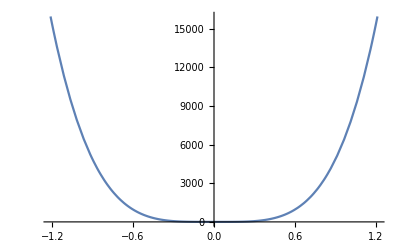

```mathematica
Plot[Energy,{ebar,-1.2129912573027755,1.2129912573027755}]
```

```mathematica
k = 3
```

3

```mathematica
E
```

ⅇ

```mathematica
36/16
```

9/4

```mathematica
Eo = lambdazerozero*k/r0^2
```

-(8 e^4)/27

```mathematica
k=3
```

3

```mathematica
Cone[t_] = 2Integrate[(perturbationterms[x]-lambdazeroone)psizerozero[x]^2,{x,-Infinity,t}]/psizerozero[t]^2
```

Set::write: Tag Cone in Cone[t_] is Protected.

ConditionalExpression[1/(180 √2 k^2 (3/4+r0^4 V''[r0])^(1/4) (3+4 r0^4 V''[r0])^(5/4))ⅇ^(1/2 t^2 √(3/4+r0^4 V''[r0])-1/4 t^2 √(3+4 r0^4 V''[r0])) (-6 √k t^4 (3+4 r0^4 V''[r0]) (-90+r0^7 V^(5)[r0])-24 √k t^2 √(3+4 r0^4 V''[r0]) (-15 (12-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+5 k r0^5 √(3+4 r0^4 V''[r0]) V^(3)[r0]+2 r0^7 V^(5)[r0])-12 √k (-1575+180 k+60 (-3+4 k) r0^4 V''[r0]+480 √(3+4 r0^4 V''[r0])-120 k √(3+4 r0^4 V''[r0])+40 k r0^5 √(3+4 r0^4 V''[r0]) V^(3)[r0]+16 r0^7 V^(5)[r0])-t^5 (3+4 r0^4 V''[r0]) (630+r0^8 V^(6)[r0])-10 t^3 √(3+4 r0^4 V''[r0]) (45 (14-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+3 k r0^6 √(3+4 r0^4 V''[r0]) V^(4)[r0]+r0^8 V^(6)[r0])-30 t (1341-108 k-36 (-3+4 k) r0^4 V''[r0]-360 √(3+4 r0^4 V''[r0])+90 k √(3+4 r0^4 V''[r0])+6 k r0^6 √(3+4 r0^4 V''[r0]) V^(4)[r0]+2 r0^8 V^(6)[r0])), Re[√(3+4 r0^4 V''[r0])]>0]

```mathematica
Cones[t_] = 1/(180 √2 k^2 (3/4+r0^4 V''[r0])^(1/4) (3+4 r0^4 V''[r0])^(5/4))ⅇ^(1/2 t^2 √(3/4+r0^4 V''[r0])-1/4 t^2 √(3+4 r0^4 V''[r0])) (-6 √k t^4 (3+4 r0^4 V''[r0]) (-90+r0^7 Derivative[5][V][r0])-24 √k t^2 √(3+4 r0^4 V''[r0]) (-15 (12-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+5 k r0^5 √(3+4 r0^4 V''[r0]) Derivative[3][V][r0]+2 r0^7 Derivative[5][V][r0])-12 √k (-1575+180 k+60 (-3+4 k) r0^4 V''[r0]+480 √(3+4 r0^4 V''[r0])-120 k √(3+4 r0^4 V''[r0])+40 k r0^5 √(3+4 r0^4 V''[r0]) Derivative[3][V][r0]+16 r0^7 Derivative[5][V][r0])-t^5 (3+4 r0^4 V''[r0]) (630+r0^8 Derivative[6][V][r0])-10 t^3 √(3+4 r0^4 V''[r0]) (45 (14-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+3 k r0^6 √(3+4 r0^4 V''[r0]) Derivative[4][V][r0]+r0^8 Derivative[6][V][r0])-30 t (1341-108 k-36 (-3+4 k) r0^4 V''[r0]-360 √(3+4 r0^4 V''[r0])+90 k √(3+4 r0^4 V''[r0])+6 k r0^6 √(3+4 r0^4 V''[r0]) Derivative[4][V][r0]+2 r0^8 Derivative[6][V][r0]))
```

1/(180 √2 k^2 (3/4+r0^4 V''[r0])^(1/4) (3+4 r0^4 V''[r0])^(5/4))ⅇ^(1/2 t^2 √(3/4+r0^4 V''[r0])-1/4 t^2 √(3+4 r0^4 V''[r0])) (-6 √k t^4 (3+4 r0^4 V''[r0]) (-90+r0^7 V^(5)[r0])-24 √k t^2 √(3+4 r0^4 V''[r0]) (-15 (12-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+5 k r0^5 √(3+4 r0^4 V''[r0]) V^(3)[r0]+2 r0^7 V^(5)[r0])-12 √k (-1575+180 k+60 (-3+4 k) r0^4 V''[r0]+480 √(3+4 r0^4 V''[r0])-120 k √(3+4 r0^4 V''[r0])+40 k r0^5 √(3+4 r0^4 V''[r0]) V^(3)[r0]+16 r0^7 V^(5)[r0])-t^5 (3+4 r0^4 V''[r0]) (630+r0^8 V^(6)[r0])-10 t^3 √(3+4 r0^4 V''[r0]) (45 (14-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+3 k r0^6 √(3+4 r0^4 V''[r0]) V^(4)[r0]+r0^8 V^(6)[r0])-30 t (1341-108 k-36 (-3+4 k) r0^4 V''[r0]-360 √(3+4 r0^4 V''[r0])+90 k √(3+4 r0^4 V''[r0])+6 k r0^6 √(3+4 r0^4 V''[r0]) V^(4)[r0]+2 r0^8 V^(6)[r0]))

```mathematica
lambdazerotwo = Integrate[Cones[x]^2psizerozero[x]^2,{x,-Infinity,Infinity}]
```

∫_(-∞)^∞ ((ⅇ^(1/2 x^2 √(3/4+r0^4 V''[r0])-1/2 x^2 √(3+4 r0^4 V''[r0])) (-6 √k x^4 (3+4 r0^4 V''[r0]) (-90+r0^7 V^(5)[r0])-24 √k x^2 √(3+4 r0^4 V''[r0]) (-15 (12-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+5 k r0^5 √(3+4 r0^4 V''[r0]) V^(3)[r0]+2 r0^7 V^(5)[r0])-12 √k (-1575+180 k+60 (-3+4 k) r0^4 V''[r0]+480 √(3+4 r0^4 V''[r0])-120 k √(3+4 r0^4 V''[r0])+40 k r0^5 √(3+4 r0^4 V''[r0]) V^(3)[r0]+16 r0^7 V^(5)[r0])-x^5 (3+4 r0^4 V''[r0]) (630+r0^8 V^(6)[r0])-10 x^3 √(3+4 r0^4 V''[r0]) (45 (14-4 √(3+4 r0^4 V''[r0])+k √(3+4 r0^4 V''[r0]))+3 k r0^6 √(3+4 r0^4 V''[r0]) V^(4)[r0]+r0^8 V^(6)[r0])-30 x (1341-108 k-36 (-3+4 k) r0^4 V''[r0]-360 √(3+4 r0^4 V''[r0])+90 k √(3+4 r0^4 V''[r0])+6 k r0^6 √(3+4 r0^4 V''[r0]) V^(4)[r0]+2 r0^8 V^(6)[r0]))^2)/(64800 k^4 √(2 π) (3/4+r0^4 V''[r0])^(1/4) (3+4 r0^4 V''[r0])^(5/2)))ⅆx